```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/josephhenderson/Desktop/Research/EquitablePartitions/Mathematica

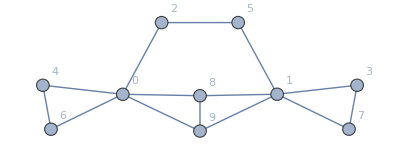

```mathematica
graph = Graph[Import["exported_graph.graphml"],VertexLabels->Automatic,VertexSize->.35]
```

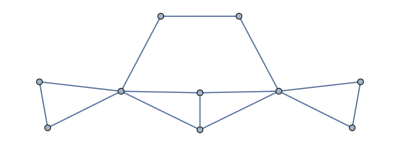

```mathematica
H = AdjacencyGraph[AdjacencyMatrix[graph]]
```

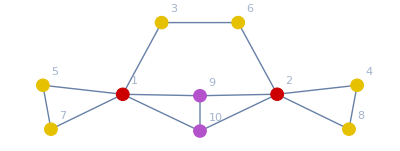

-Graphics-

```mathematica
HighlightGraph[H,{{2,1},{3,4,5,6,7,8},{9,10}},VertexSize->.35,VertexLabels->Automatic]
```